Inlämningsuppgift 3
Jerry Cheung & Daniel Westerlund


Trafikflöde
Problem:
Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett  viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Till exempel om flödet in till en fyrvägs korsning är x_1 fordon/tidsenhet respektive 30 fordon/tidsenhet och flödet ut från korsningen är x_2 fordon/tidsenhet respektive 50 fordon/tidsenhet, så gäller det att x_1+30=x_2+50 eller x_1-x_2=20. Varje korsning ger alltså en linjärekvation i okända flöden x_n. Om man löser ekvationssystemet så kan man bestämma flödet genom trafiksystemet.

Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
Antagade  kan antas bevara giltigt så länge som inga bilar stannar i korsningar och skapar trafikstockning. Vi antar att trafiket flöder endast i pilarnas riktning, att  pilarna symboliserar att det är enkelriktad. 
   
Vilka andra förenklingar har vi antagit?
Vi har antagit att det är samma hastighet på alla väger, i teorin skulle alla bilar kunna välja antingen x1 eller x2, och att det blir trafikstokning någonstans

Ekvationssystem för trafikflödet  
x1 + x2 = 200
x1 = 40+ x3 +x4
x4 + x5 = 60  
x2 + x3 = 100 + x5 

Bestäm trafikflödet för vägsystemet.
Trafikflödet in i första korsningen är 200, detta gör att 200bilar kommer att åka antingen till x1 eller x2 där minst 40 bilar åker till x1. Från x1 är det 40 bilar är i utflödet och resterande bilar från x1 åker antingen till x3 eller x4. De bilar som åker till x4 blir tillsammans med x5 utflödet 60. De bilar som åker till x3 åker antingen till utflödet 100 eller till x5. De bilar som åker till x5 bildar tillsammans med x4 utflödet 60. 

Hur ändras trafikflödet om  x_4 är noll ?
Om x4 är noll, kommer det tvinga trafikflödet att minst 40 bilar tar x1, och därefter blir utflöde. Resterande bilar måste åka via korsningen x2,x3,x5. Detta gör att den korsningen blir hårt trafikerad och bilarna får inget val. 


Antag att trafiken måste flyta i de riktningar som anges i figuren. Om x_4 är noll vad är då minsta värdet på x_1?
x1 måste vara minst 40, för annars kan inte utflödet vara 40.

Kaniner
Problem:
Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

Beräkna talföljden och rita en graf över den.

{1,1,2,3,5,8,13,21,34,55}

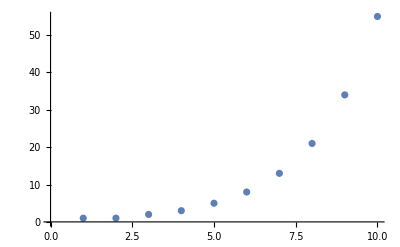

{2,3,5,8,13,21,34,55}

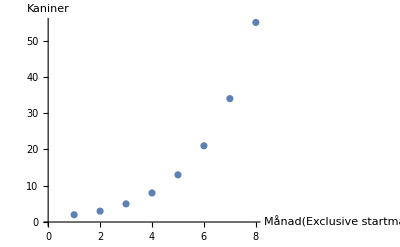

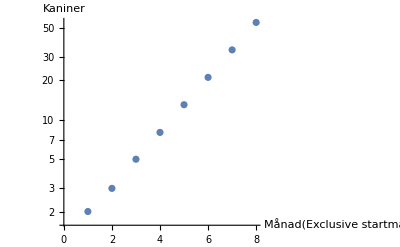

{1.17228,0.481043}

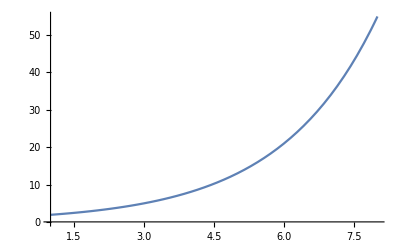

{1,2,3,4,5,6,7,8}

{{1,2},{2,3},{3,5},{4,8},{5,13},{6,21},{7,34},{8,55}}

-Graphics-

```mathematica
p1 = Table[Fibonacci[n],{n,10}]

ListPlot[p1]
p2 = p1[[3;;10]]
ListPlot[p2, AxesLabel->{Månad [Exclusive startmånader],Kaniner}]
ListLogPlot[p2, AxesLabel->{Månad [Exclusive startmånader],Kaniner}]
{a1,b1}={a,b}/.FindFit[p2,{a×ⅇ^(b*k)},{a,b},k]
p3 = Plot[a1*ⅇ^(b1*k), {k,1,8}]
p4 = Range[8]
p5 = Transpose[{p4,p2}]
ListPlot[p5, AxesLabel->{Månad[Exclusive startmånader],Kaniner}]
```

Undersök talföljden och diskutera tillväxtakten.
  Vi anser att de två första värdena, p1 = 1 och p2 = 2  inte borde visas på grafen eftersom det är initialvärdena och det börjar egentligen vid p3, som är den första "riktiga" månaden.  
  Talföljden räknar inte med någon snitt ålder för kaninerna då de dör en naturlig död, och således verkar den inte räkna med ett bortfall av kaniner som har dött. 
  Vilket gör att den får en högre tillväxt. Som man ser på grafen är det en expotionell funktion, och den ökar väldigt kraftigt, undersökar man talföljden ser man att antalet kaniner en 
  specifik månad är summan av de två förgående månaderna.  

Vilka begränsningar har modellen:
Den räknar inte med bortfall utav kaniner, vilket gör att om man kollar efter väldigt lång tid, kommer de första kaninera vara med i uträkningen som kaniner som föder nya kaniner. 
Detta gör att modellen endast är någolunda giltig tills att de två första kaninera sluta producera nya kaniner.  

Hur kan man förbättra modellen:
Genom att begräna modellen över en kanin reproducerings period under livet. 
Räkna fram något snitt bortfall av kaniner över tid.